# Using DiscKosky

DiscKosky is a package for studying the repeated discontinuity structure of Euler integrals. This is done primarily by counting the number of critical points associated to the Feynman integral.

This tech note introduces the most important commands of DiscKosky, illustrated on a simple one-loop example. More details on each function and its options can be found on the corresponding reference pages.

Load the package:

```mathematica
Needs["DiscKosky`"]
```

## Core Usage

DiscKosky provides three main high-level functions for predicting sequential discontinuities: CheckDoubleDiscontinuities, CheckSequentialDiscontinuity, and SectorDropGraph.

CheckDoubleDiscontinuities[g,vars,sings] | matrix indicating which ordered pairs of discontinuities with respect to the singularities sings can appear
CheckSequentialDiscontinuity[g,vars,sings,seq] | test whether the sequence of discontinuities with respect to the singularities indexed by seq can appear
SectorDropGraph[g,vars,sings] | graph of the sectors of the integral, labeled by the singularities that appear in each sector

High-level functions for predicting sequential discontinuities.

The three inputs needed to apply these functions to a given Feynman integral are the Lee–Pomeransky polynomial, a list of the integration variables, and a candidate set of singular loci in the space of external parameters. For example, consider the two-mass easy box integral shown below.

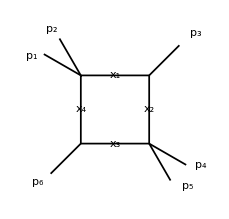

Two-mass easy box integral. Each propagator is labeled by its integration variable.

The kinematic variables of this integral are the masses of the two massive corners, m_1^2=(p_1+p_2)^2 and m_2^2=(p_4+p_5)^2, and the invariants s_12=(p_1+p_2+p_3)^2 and s_23=(p_3+p_4+p_5)^2.

For this integral, the Lee–Pomeransky polynomial, the integration variables, and the candidate singularities are given by:

```mathematica
g=x1+x2+x3-s23 x1 x3-m2^2 x2 x3+x4-m1^2 x1 x4-s12 x2 x4;
vars={x1,x2,x3,x4};
sings={s23,m1,m2,s12,-m1^2+s23,-m2^2+s23,m2^2-s12,m1^2-s12,m1^2 m2^2-s12 s23,-m1^2-m2^2+s12+s23};
```

### Double Discontinuities

Given these arguments, CheckDoubleDiscontinuities produces a matrix that tells the user which ordered sequences of discontinuities can appear in the Feynman integral.

Compute the double discontinuity matrix and display it in matrix form:

```mathematica
dM1=CheckDoubleDiscontinuities[g,vars,sings];
```

```mathematica
dM1//MatrixForm
```

(True | False | False | False | Indeterminate | Indeterminate | False | False | True | True
False | True | False | False | Indeterminate | False | False | Indeterminate | True | True
False | False | True | False | False | Indeterminate | Indeterminate | False | True | True
False | False | False | True | False | False | Indeterminate | Indeterminate | True | True
False | False | False | False | Indeterminate | False | False | False | True | True
False | False | False | False | False | Indeterminate | False | False | True | True
False | False | False | False | False | False | Indeterminate | False | True | True
False | False | False | False | False | False | False | Indeterminate | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True)

Here Indeterminate indicates that a higher-dimensional solution to the critical point equations has been found. The entry in the i^th row and j^th column of this matrix, namely dM1⟦i,j⟧, tells us whether a discontinuity with respect to the j^th singularity can follow a discontinuity with respect to the i^th singularity. Namely, if dM1⟦i,j⟧ is False, this indicates that the Feynman integral ℐ satisfies a genealogical constraint of the form

Disc_sings⟦j⟧⋯Disc_sings⟦i⟧⋯ℐ=0

Conversely, if dM1⟦i,j⟧ is True, such sequences of discontinuities are not ruled out by this method.

### Refining Indeterminate Entries

When dM1⟦i,j⟧ is Indeterminate, there are two ways one can proceed. Most directly, these entries indicate that the critical point algorithm cannot be applied, so the conservative option is to treat such a result as equivalent to True. However, more can be said in many of the cases in which Indeterminate solutions arise (such as when a sector that has no critical points in generic kinematics becomes Indeterminate in a singular limit). These more refined predictions can be requested by using the option "RefineIndeterminates", which can be passed to all of the core DiscKosky functions.

Compute the double discontinuity matrix with "RefineIndeterminates" enabled:

```mathematica
dM2=CheckDoubleDiscontinuities[g,vars,sings,"RefineIndeterminates"->True];
```

```mathematica
dM2//MatrixForm
```

(True | False | False | False | True | True | False | False | True | True
False | True | False | False | True | False | False | True | True | True
False | False | True | False | False | True | True | False | True | True
False | False | False | True | False | False | True | True | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True
False | False | False | False | False | False | False | False | True | True)

Compared to dM1, four new singularities (sings⟦5⟧, sings⟦6⟧, sings⟦7⟧, and sings⟦8⟧) can now be identified as giving rise to non-repeating discontinuities. Any Indeterminate entries that the refined algorithm cannot resolve are conservatively set to True.

### Sequences of Discontinuities

The function CheckSequentialDiscontinuity works in a very similar manner, except that it tests for a specific string of discontinuities of any length. It takes four inputs: the same three as above, and a specific sequence to test, given as a list of positions in sings.

Test whether discontinuities with respect to sings⟦3⟧, sings⟦9⟧, and sings⟦7⟧ can appear in this order:

```mathematica
CheckSequentialDiscontinuity[g,vars,sings,{3,9,7},"RefineIndeterminates"->True]
```

False

This result implies that

Disc_sings⟦7⟧⋯Disc_sings⟦9⟧⋯Disc_sings⟦3⟧⋯ℐ=0

### Sector Drop Graphs

The information given by the above functions can also be displayed graphically with the command SectorDropGraph.

Draw the sector drop graph of the two-mass easy box:

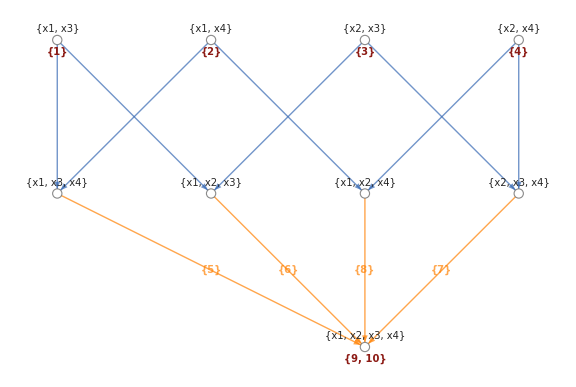

```mathematica
SectorDropGraph[g,vars,sings,"RefineIndeterminates"->True]
```

Each node in this graph represents the sector of the Feynman integral corresponding to the integration variables that appear above it (for instance, the top-left node, labeled by {x1,x3}, corresponds to the sector defined by x_2=x_4=0); the indices of the singularities that appear in each of these sectors are displayed below the node. Allowed sequences of discontinuities can be read off from this graph by either choosing a singularity at the current node, or one that can be reached by following any sequence of directed arrows. If the option "RefineIndeterminates" is enabled, some singularities may be placed on edges (marked in orange). These represent non-repeating discontinuities.

## Other Useful Functions

DiscKosky also exposes some lower-level functions that can be used to identify nonzero sequences of discontinuities.

CountSectorsUnregulated[g,vars,cut] | number of critical points in each sector compatible with the cut propagators cut
CountSectorsRegulated[g,vars,cut] | number of critical points computed with analytic regulators
FindSingularitySectors[g,vars,sings,i] | sectors associated with the singularity sings⟦i⟧

Lower-level functions for counting critical points and locating singularities.

### Counting Critical Points

The first of these is CountSectorsUnregulated, which computes the number of critical points in each sector. It takes as input a Lee–Pomeransky polynomial, a list of integration variables, and a set of propagators to cut. The result is the number of critical points in each sector above the specified cut. The output of this function closely mirrors that of the Mint package.

Count the critical points of the two-mass easy box, with no propagators cut:

```mathematica
CountSectorsUnregulated[g,vars,{}]
```

{5,{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1},{{},{x1},{x2},{x3},{x4},{x1,x2},{x1,x3},{x1,x4},{x2,x3},{x2,x4},{x3,x4},{x1,x2,x3},{x1,x2,x4},{x1,x3,x4},{x2,x3,x4},{x1,x2,x3,x4}}}

The first element of the output is the total number of critical points (summed over all sectors that are consistent with the specified cut), while the second indicates how these critical points are distributed among the different sectors. The third element gives the list of sectors that label the critical point counts in the second element.

If a non-empty cut is specified, the function simply ignores any sectors that do not survive on the support of that cut.

Count only the critical points that survive when all four propagators are cut:

```mathematica
CountSectorsUnregulated[g,vars,{x1,x2,x3,x4}]
```

{1,{1},{{x1,x2,x3,x4}}}

In many cases, these critical points can be interpreted as the number of master integrals in a given sector. However, this number is known to sometimes undercount. When combined with the possibility of magic relations, a naive interpretation of this result must be taken with caution. An explicit example of such an undercount is given in the Possible Issues section of the reference page of CountSectorsUnregulated.

### Kinematic Constraints

CountSectorsUnregulated also supports the computation of critical points on the support of kinematic constraints, via the "Constraint" option.

Count the critical points in the top sector on the locus s_12+s_23-m_1^2-m_2^2=0:

```mathematica
CountSectorsUnregulated[g,vars,{x1,x2,x3,x4},"Constraint"->sings⟦10⟧]
```

{0,{0},{{x1,x2,x3,x4}}}

This shows that one critical point is lost in the top sector when the condition sings⟦10⟧=s_12+s_23-m_1^2-m_2^2=0 is enforced on the external kinematics. This indicates that the corresponding Lefschetz thimble can play the role of a vanishing cycle when a discontinuity is computed with respect to the singularity at s_12+s_23-m_1^2-m_2^2=0.

### Sectors Associated with a Singularity

It is also possible to access directly which on-shell lines (sectors) correspond to a singularity with the command FindSingularitySectors. This command takes as input a Lee–Pomeransky polynomial, a list of integration variables, the set of candidate Landau singularities, and the index of the specific singularity to analyze.

Find the sectors associated with the singularity sings⟦10⟧:

```mathematica
FindSingularitySectors[g,vars,sings,10]
```

{{x1,x2,x3,x4}}

This shows that the singularity at s_12+s_23-m_1^2-m_2^2=0 is associated with (only) the top sector of the one-loop box.

### Counting with Analytic Regulators

Finally, DiscKosky provides a public function for counting with analytic regulators. More precisely, CountSectorsRegulated computes the Euler characteristic χ(ℂ^n∖V(x_1⋯x_n G)), where G is the Lee–Pomeransky polynomial. This can always be interpreted as the number of master integrals of the (regulated) Feynman integral. In most cases, the output of CountSectorsUnregulated will agree with this more rigorous computation.

Compare the total number of critical points from the unregulated and regulated counts:

```mathematica
CountSectorsUnregulated[g,vars,{}]⟦1⟧
```

5

```mathematica
CountSectorsRegulated[g,vars,{}]
```

5

CountSectorsRegulated also supports the "Constraint" option, in the same way as CountSectorsUnregulated.

Related Guides

DiscKosky

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Tech Note

DiscKosky

DiscKosky`

DiscKosky/tutorial/UsingDiscKosky

### Keywords

DiscKosky, sequential discontinuities, genealogical constraints, critical points, Landau singularities, Lee-Pomeransky polynomial, sectors, master integrals